```mathematica
DateDifferenceInUnits[date1_DateObject,date2_DateObject,unit_]:=QuantityMagnitude[DateDifference[date1,date2,unit]]
```

```mathematica
PrecedingVal[list_,val_]:=Module[
{nearestVal,nearestPos},
nearestVal=Nearest[list,val][[1]];
nearestPos=Position[list,nearestVal][[1]][[1]];
If[
nearestVal<val,
nearestVal,
list[[nearestPos-1]]
]
]
```

```mathematica
PrecedingPos[list_,val_]:=Module[
{nearestVal,nearestPos},
nearestVal=Nearest[list,val][[1]];
nearestPos=Position[list,nearestVal][[1]][[1]];
If[
nearestVal<val,
nearestPos,
nearestPos-1
]
]
```

```mathematica
SparseTimeMovingAverage[data_List,windowSize_?NumericQ]:=Module[{times,values,averageValues,result,halfWindow,timeWindowIndices},(*Extract times and values*){times,values}=Transpose[data];
(*Half of the window size*)halfWindow=windowSize/2;
(*Moving average calculation*)averageValues=Table[(*Find indices of times within the window around the current time point*)timeWindowIndices=Flatten[Position[times,_?(Abs[#-times[[i]]]<=halfWindow&)]];
If[Length[timeWindowIndices]>0,Mean[values[[timeWindowIndices]]],(*Calculate mean if indices are found*)values[[i]] (*Use current value if no other values are in the window*)],{i,Length[times]}];
(*Combine times with calculated averages*)result=Transpose[{times,averageValues}]]
```

```mathematica
voltageTimestamps=StringSplit[Import[NotebookDirectory[]<>"gas_pulse_times.txt"],"\n"];
```

```mathematica
startDate=DateObject[voltageTimestamps[[1]]]
```

Wed 22 Nov 2023 17:11:33GMT+1

```mathematica
timeGranularity="Second";
```

```mathematica
voltageTimes=Map[
Round[DateDifferenceInUnits[startDate,DateObject[#],timeGranularity]]
&,voltageTimestamps];
```

```mathematica
Select[Differences[voltageTimes],60<#&]
```

{61,266,136,119,92,147,254,114,110,110,110,185,70,79,93,206,132,136,229,68,71,86,87,94,99,107,105,253,75,354,275,67,88,100,99,116,848,135,83,84,78,119,168,167,88,90,99,136,99,120,83,149,80,90,93,100,108,108,313,170,86,140,70,97}

```mathematica
Flatten[Map[Position[Differences[voltageTimes],#]&,Select[Differences[voltageTimes],60<#&]]]
```

{{{9}},{{10}},{{18},{142},{475}},{{27},{297}},{{28}},{{57}},{{76}},{{85}},{{93},{101},{110}},{{93},{101},{110}},{{93},{101},{110}},{{111}},{{114},{556}},{{118}},{{123},{509}},{{128}},{{135}},{{18},{142},{475}},{{150}},{{155}},{{158}},{{162},{549}},{{167}},{{172}},{{177},{233},{431},{484}},{{182}},{{188}},{{194}},{{195}},{{204}},{{214}},{{219}},{{223},{422}},{{228},{514}},{{177},{233},{431},{484}},{{238}},{{241}},{{286}},{{287},{488}},{{290}},{{293}},{{27},{297}},{{306}},{{315}},{{223},{422}},{{426},{504}},{{177},{233},{431},{484}},{{18},{142},{475}},{{177},{233},{431},{484}},{{485}},{{287},{488}},{{494}},{{499}},{{426},{504}},{{123},{509}},{{228},{514}},{{519},{525}},{{519},{525}},{{531}},{{539}},{{162},{549}},{{552}},{{114},{556}},{{560}}}

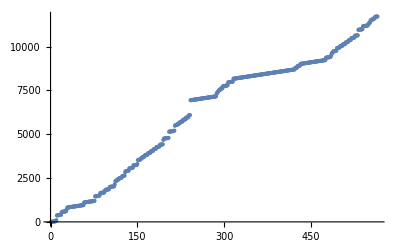

```mathematica
ListPlot[pulseTimes]
```

```mathematica
Differences[pulseTimes]
```

{0.0833333,0.0833333,0.0833333,0.0833333,0.1,0.0833333,0.0833333,0.0833333,1.01667,4.43333,0.0833333,0.0833333,0.0833333,0.1,0.0833333,0.0833333,0.0833333,2.26667,0.533333,0.0833333,0.1,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,1.98333,1.53333,0.0833333,0.1,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.1,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,2.45,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.1,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.1,4.23333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.75,1.9,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,1.83333,0.616667,0.0833333,0.1,0.0833333,0.0833333,0.0833333,0.0833333,1.83333,0.45,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,1.83333,3.08333,0.0833333,0.0833333,1.16667,0.0833333,0.0833333,0.0833333,1.31667,0.0833333,0.0833333,0.0833333,0.1,1.55,0.0833333,0.0833333,0.0833333,0.0833333,3.43333,0.9,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,2.2,0.0833333,0.0833333,0.0833333,0.0833333,0.1,0.0833333,2.26667,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.866667,3.81667,0.0833333,0.0833333,0.0833333,0.0833333,1.13333,0.1,0.0833333,1.18333,0.0833333,0.0833333,0.0833333,1.43333,0.0833333,0.0833333,0.0833333,0.0833333,1.45,0.0833333,0.0833333,0.0833333,0.0833333,1.56667,0.0833333,0.0833333,0.0833333,0.0833333,1.65,0.0833333,0.1,0.0833333,0.0833333,1.78333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,1.75,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,4.21667,1.25,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,5.9,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.383333,4.58333,0.583333,0.0833333,0.0833333,0.0833333,1.11667,0.0833333,0.0833333,0.0833333,1.46667,0.0833333,0.1,0.0833333,0.0833333,1.66667,0.0833333,0.0833333,0.0833333,0.0833333,1.65,0.0833333,0.0833333,0.1,0.0833333,1.93333,0.0833333,0.0833333,14.1333,0.0833333,0.0833333,0.0833333,0.0833333,0.1,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.1,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.1,2.25,1.38333,0.6,0.25,1.4,0.0833333,0.0833333,1.3,0.0833333,0.0833333,0.0833333,1.98333,0.0833333,0.0833333,0.0833333,0.0833333,0.3,0.0833333,0.0833333,0.0833333,2.8,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,2.78333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.1,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.1,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.1,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.1,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,1.46667,0.0833333,0.0833333,0.1,1.5,0.0833333,0.0833333,0.0833333,0.0833333,1.65,0.0833333,0.1,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.1,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.1,0.0833333,0.0833333,0.0833333,2.26667,0.0833333,0.0833333,0.0833333,0.1,0.0833333,0.0833333,0.0833333,0.0833333,1.65,2.,0.25,0.266667,1.38333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,2.48333,0.0833333,0.0833333,0.0833333,0.0833333,1.33333,0.0833333,0.0833333,0.0833333,0.0833333,1.5,0.0833333,0.0833333,0.0833333,0.0833333,1.55,0.0833333,0.0833333,0.1,0.0833333,1.66667,0.0833333,0.0833333,0.0833333,0.0833333,1.8,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,1.8,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,5.21667,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,2.83333,0.0833333,0.0833333,0.1,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.7,1.43333,0.2,0.3,2.33333,0.0833333,0.0833333,0.0833333,1.16667,0.0833333,0.1,0.0833333,1.61667,0.0833333,0.0833333,0.0833333,0.0833333}

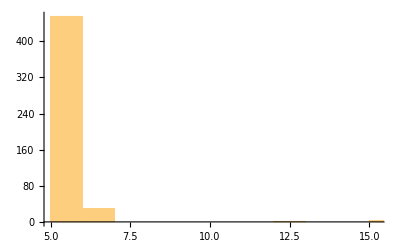

```mathematica
Histogram[Differences[pulseTimes]]
```

```mathematica
pulseTimes[[1]]
```

0.

```mathematica
pulseTimes//Length
```

3.25551

```mathematica
Map[pulseTimes[[1;;10]]
```

{0.,5.16457,10.2141,15.3232,20.494,25.6641,30.6734,35.7624,40.8115,101.985}

```mathematica
SparseArray[m]
```

SparseArray[…]

```mathematica
?SparseArray
```

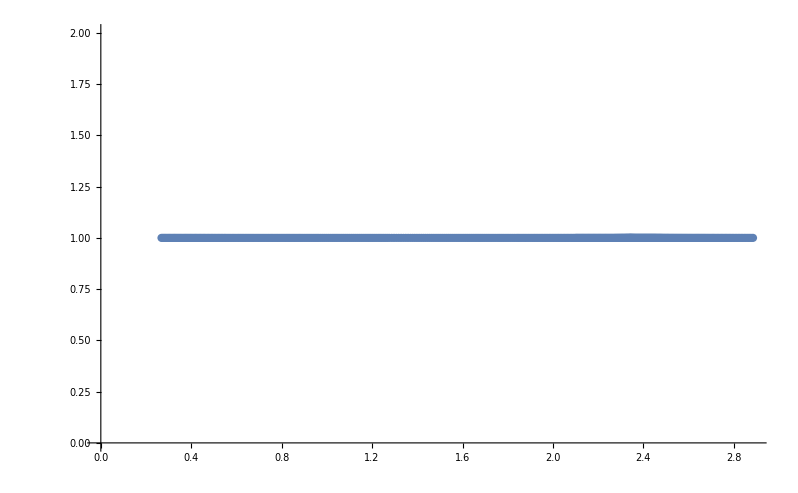

```mathematica
ListPlot[MovingAverage[Transpose[{pulseTimes,ConstantArray[1,Length[pulseTimes]]}],100]]
```